```mathematica
<<"/home/tony/Research/AbaciSymmetricFunctions.m"
DegreeOfRep[L_]:=Total[L]!/(Times@@HookLengths@L)
```

```mathematica
ModHookCells[λ_,k_]:=Graphics@Flatten[RowOfText@@@Transpose@{Reverse/@HookRows@λ,Range@Length@λ}/.Text[a_,{b_,c_}]->{If[Mod[a,k]==0,{Red,Opacity[1]},{Black,Opacity[.25]}],Text[a,{b,c}]}]
ModHookFerrers[λ_,k_]:=Show[Ferrers@λ,ModHookCells[λ,k]]
```

```mathematica
AbaciToPartition[a_,λ_:{}]:=If[a=={},λ,
If[MemberQ[a,0],
Module[{p=First@FirstPosition[a,0]},AbaciToPartition[a[[p+1;;]],Join[λ,Table[Count[a,0],p-1]]]],
Join[λ,Table[0,Length@a]]]]
AbaciRunners[a_,p_]:=Transpose@Partition[PadLeft[a,p Ceiling[Length[a]/p]],p]
```

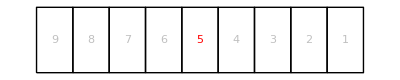
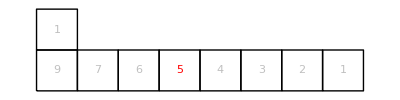
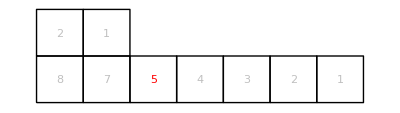
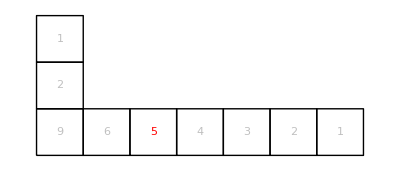
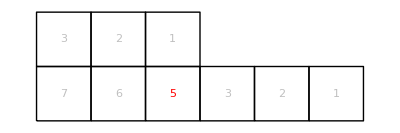
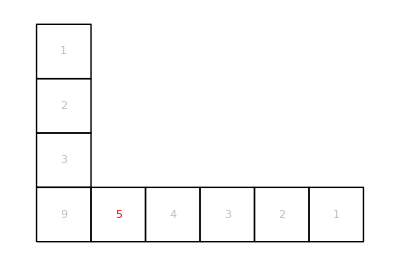
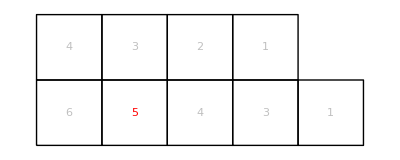
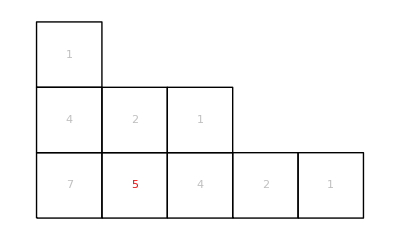
({9} | -Graphics- | {1,0,0,0,0,0,0,0,0,0} | (1 | 0
0 | 0
0 | 0
0 | 0
0 | 0)
{8,1} | -Graphics- | {1,0,0,0,0,0,0,0,1,0} | (1 | 0
0 | 0
0 | 0
0 | 1
0 | 0)
{7,2} | -Graphics- | {1,0,0,0,0,0,1,0,0} | (0 | 0
1 | 0
0 | 1
0 | 0
0 | 0)
{7,1,1} | -Graphics- | {1,0,0,0,0,0,0,1,1,0} | (1 | 0
0 | 0
0 | 1
0 | 1
0 | 0)
{6,3} | -Graphics- | {1,0,0,0,1,0,0,0} | (0 | 0
0 | 1
1 | 0
0 | 0
0 | 0)
{6,1,1,1} | -Graphics- | {1,0,0,0,0,0,1,1,1,0} | (1 | 0
0 | 1
0 | 1
0 | 1
0 | 0)
{5,4} | -Graphics- | {1,0,1,0,0,0,0} | (0 | 1
0 | 0
0 | 0
1 | 0
0 | 0)
{5,3,1} | -Graphics- | {1,0,0,1,0,0,1,0} | (0 | 1
0 | 0
1 | 0
0 | 1
0 | 0)
{5,2,1,1} | -Graphics- | {1,0,0,0,1,0,1,1,0} | (0 | 1
1 | 0
0 | 1
0 | 1
0 | 0)
{4,4,1} | -Graphics- | {1,1,0,0,0,1,0} | (0 | 0
0 | 0
0 | 0
1 | 1
1 | 0)
{4,3,2} | -Graphics- | {1,0,1,0,1,0,0} | (0 | 1
0 | 0
0 | 1
1 | 0
0 | 0)
{4,3,1,1} | -Graphics- | {1,0,1,0,0,1,1,0} | (0 | 0
0 | 0
1 | 1
0 | 1
1 | 0)
{4,2,2,1} | -Graphics- | {1,0,0,1,1,0,1,0} | (0 | 1
0 | 1
1 | 0
0 | 1
0 | 0)
{4,2,1,1,1} | -Graphics- | {1,0,0,1,0,1,1,1,0} | (0 | 0
1 | 1
0 | 1
0 | 1
1 | 0)
{4,1,1,1,1,1} | -Graphics- | {1,0,0,0,1,1,1,1,1,0} | (1 | 1
0 | 1
0 | 1
0 | 1
1 | 0)
{3,3,3} | -Graphics- | {1,1,1,0,0,0} | (0 | 1
0 | 1
0 | 0
0 | 0
1 | 0)
{3,3,2,1} | -Graphics- | {1,1,0,1,0,1,0} | (0 | 0
0 | 1
0 | 0
1 | 1
1 | 0)
{3,2,2,2} | -Graphics- | {1,0,1,1,1,0,0} | (0 | 1
0 | 1
0 | 1
1 | 0
0 | 0)
{3,2,2,1,1} | -Graphics- | {1,0,1,1,0,1,1,0} | (0 | 1
0 | 0
1 | 1
0 | 1
1 | 0)
{3,1,1,1,1,1,1} | -Graphics- | {1,0,0,1,1,1,1,1,1,0} | (1 | 1
0 | 1
0 | 1
1 | 1
1 | 0)
{2,2,2,2,1} | -Graphics- | {1,1,1,1,0,1,0} | (0 | 1
0 | 1
0 | 0
1 | 1
1 | 0)
{2,2,2,1,1,1} | -Graphics- | {1,1,1,0,1,1,1,0} | (0 | 0
0 | 1
1 | 1
1 | 1
1 | 0)
{2,2,1,1,1,1,1} | -Graphics- | {1,1,0,1,1,1,1,1,0} | (0 | 1
1 | 1
1 | 1
0 | 1
1 | 0)
{2,1,1,1,1,1,1,1} | -Graphics- | {1,0,1,1,1,1,1,1,1,0} | (1 | 1
0 | 1
1 | 1
1 | 1
1 | 0)
{1,1,1,1,1,1,1,1,1} | -Graphics- | {1,1,1,1,1,1,1,1,1,0} | (1 | 1
1 | 1
1 | 1
1 | 1
1 | 0))

```mathematica
p=5;
({#,ModHookFerrers[#,p],PartitionToAbaci@#,MatrixForm@AbaciRunners[PartitionToAbaci@#,p]}&/@Select[IntegerPartitions@9,Mod[DegreeOfRep@#,p]!=0&])//MatrixForm
```

```mathematica
Core[λ_,p_]:=Cases[AbaciToPartition@Flatten@Transpose[AbaciRunners[PartitionToAbaci@λ,p]//.{{x___,1,y___,0,z___}->{x,0,y,1,z}}],_?Positive]
```

```mathematica
p=13;
(Core[#,p]&/@Select[IntegerPartitions@25,Mod[DegreeOfRep@#,p]!=0&])//Tally
```

{{{12},13},{{11,1},13},{{10,2},13},{{10,1,1},13},{{9,3},13},{{9,2,1},13},{{9,1,1,1},13},{{8,4},13},{{8,3,1},13},{{8,2,2},13},{{8,2,1,1},13},{{8,1,1,1,1},13},{{7,5},13},{{7,4,1},13},{{7,3,2},13},{{7,3,1,1},13},{{7,2,2,1},13},{{7,2,1,1,1},13},{{7,1,1,1,1,1},13},{{6,6},13},{{6,5,1},13},{{6,4,2},13},{{6,4,1,1},13},{{6,3,3},13},{{6,3,2,1},13},{{6,3,1,1,1},13},{{6,2,2,2},13},{{6,2,2,1,1},13},{{6,2,1,1,1,1},13},{{6,1,1,1,1,1,1},13},{{5,5,2},13},{{5,5,1,1},13},{{5,4,3},13},{{5,4,2,1},13},{{5,4,1,1,1},13},{{5,3,3,1},13},{{5,3,2,2},13},{{5,3,2,1,1},13},{{5,3,1,1,1,1},13},{{5,2,2,2,1},13},{{5,2,2,1,1,1},13},{{5,2,1,1,1,1,1},13},{{5,1,1,1,1,1,1,1},13},{{4,4,4},13},{{4,4,3,1},13},{{4,4,2,2},13},{{4,4,2,1,1},13},{{4,4,1,1,1,1},13},{{4,3,3,2},13},{{4,3,3,1,1},13},{{4,3,2,2,1},13},{{4,3,2,1,1,1},13},{{4,3,1,1,1,1,1},13},{{4,2,2,2,2},13},{{4,2,2,2,1,1},13},{{4,2,2,1,1,1,1},13},{{4,2,1,1,1,1,1,1},13},{{4,1,1,1,1,1,1,1,1},13},{{3,3,3,3},13},{{3,3,3,2,1},13},{{3,3,3,1,1,1},13},{{3,3,2,2,2},13},{{3,3,2,2,1,1},13},{{3,3,2,1,1,1,1},13},{{3,3,1,1,1,1,1,1},13},{{3,2,2,2,2,1},13},{{3,2,2,2,1,1,1},13},{{3,2,2,1,1,1,1,1},13},{{3,2,1,1,1,1,1,1,1},13},{{3,1,1,1,1,1,1,1,1,1},13},{{2,2,2,2,2,2},13},{{2,2,2,2,2,1,1},13},{{2,2,2,2,1,1,1,1},13},{{2,2,2,1,1,1,1,1,1},13},{{2,2,1,1,1,1,1,1,1,1},13},{{2,1,1,1,1,1,1,1,1,1,1},13},{{1,1,1,1,1,1,1,1,1,1,1,1},13}}